# Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

# Help

## 0. GetGraph

```mathematica
??GetGraph
```

```mathematica
g=GetGraph[10]
```

-Graphics-

## 1. GetDaG - удаление циклов

```mathematica
??GetDAG
```

```mathematica
GetDAG[g,ApproachOption->"Unknown"]
```

GetDAG::option: Option Unknown is not in list of options. Choose another one from the list: 
Random Order
BFS Order
DFS Order
VertexOutDegree Order
Cycle Removal
IP SCF
IP TI

$Aborted

```mathematica
GetDAG[g,ApproachOption->"Random Order"]
```

<|acyclic graph→{4->2,4->3,5->7,7->3,8->2,9->1,9->2,9->4,9->8,10->3},feedback set→{1->7,2->1,2->5,2->7,3->6,4->7,6->10,7->9,8->3,8->4,8->6,8->9,10->5}|>

```mathematica
GetDAG[g,ApproachOption->"BFS Order"]
```

<|acyclic graph→{1->7,2->5,3->6,6->10,7->3,7->9,9->2,9->4,9->8,10->5},feedback set→{2->1,2->7,4->2,4->3,4->7,5->7,8->2,8->3,8->4,8->6,8->9,9->1,10->3}|>

```mathematica
GetDAG[g,ApproachOption->"DFS Order"]
```

<|acyclic graph→{5->7,6->10,7->9,9->1,9->2,9->4,9->8,10->3,10->5},feedback set→{1->7,2->1,2->5,2->7,3->6,4->2,4->3,4->7,7->3,8->2,8->3,8->4,8->6,8->9}|>

```mathematica
GetDAG[g,ApproachOption->"VertexOutDegree Order"]
```

<|acyclic graph→{2->1,2->5,2->7,4->2,4->3,4->7,7->3,8->2,8->3,8->4,8->6,8->9,9->1,9->2,9->4,10->3,10->5},feedback set→{1->7,3->6,5->7,6->10,7->9,9->8}|>

```mathematica
step1=GetDAG[g,ApproachOption->"Cycle Removal"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8}|>

```mathematica
GetDAG[g,ApproachOption->"IP SCF"]
```

<|acyclic graph→{1->7,2->1,2->5,2->7,4->2,4->3,4->7,5->7,6->10,7->3,8->2,8->3,8->4,8->6,9->1,9->2,9->4,9->8,10->3,10->5},feedback set→{3->6,7->9,8->9}|>

```mathematica
GetDAG[g,ApproachOption->"IP TI"]
```

<|acyclic graph→{2->1,4->2,4->3,4->7,5->7,8->2,8->3,8->4,8->6,8->9,9->1,9->2,9->4,10->3,10->5},feedback set→{1->7,2->5,2->7,3->6,6->10,7->3,7->9,9->8}|>

## 2. GetLayering

```mathematica
??GetLayering
```

```mathematica
GetLayering[step1,ApproachOption->"Unknown"]
```

GetLayering::option: Option Unknown is not in list of options. Choose another one from the list: 
Longest Path
Exact
Min Width

$Aborted

```mathematica
step2=GetLayering[step1,ApproachOption->"Longest Path"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}}|>

```mathematica
GetLayering[step1,ApproachOption->"Exact"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}}|>

```mathematica
GetLayering[step1,ApproachOption->"Min Width"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2}]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->"Unk"]
```

GetLayering::option: Option Unk is not in list of options. Choose another one from the list: 
True
False

$Aborted

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->True]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10,5},{7,3,9},{1,6}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->False]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}}|>

## 3. AddDummyVertices

```mathematica
??AddDummyVertices
```

```mathematica
AddDummyVertices[step2,ApproachOption->"Unk"]
```

AddDummyVertices::option: Option Unk is not in list of options. Choose another one from the list: 
Base
Cut

$Aborted

```mathematica
AddDummyVertices[step2,ApproachOption->"Base"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,11->12,12->13,13->1,2->14,14->7,4->15,15->16,16->17,17->3,4->18,18->19,19->7,8->20,20->2,8->21,21->22,22->23,23->24,24->3,8->25,25->26,26->27,27->28,28->29,29->6,8->30,30->31,31->32,32->33,33->9,10->34,34->35,35->3,7->36,36->1,10->37,37->38,38->39,39->6,2->40,40->41,41->9,4->42,42->43,43->44,44->9},layers with dummies→{{8},{4,20,21,25,30},{2,10,15,18,22,26,31,42},{5,11,14,16,19,23,27,32,34,37,40,43},{7,12,17,24,28,33,35,38,41,44},{3,9,13,29,36,39},{6,1}},first dummy→11|>

```mathematica
step3=AddDummyVertices[step2,ApproachOption->"Cut"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},layers→{{8},{4},{2,10},{5},{7},{3,9},{1,6}},first dummy→11,layers with dummies→{{8},{4,16,20,21,26},{2,10,14,17,22,27},{5,11,15,18,23,28},{7,12,19,24,29},{3,9,13,25},{6,1}},graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,7->13,11->12,12->13,13->1,2->15,4->14,14->15,15->7,4->17,8->16,10->18,16->17,17->18,18->19,19->3,8->20,20->2,8->21,10->23,21->22,22->23,23->24,24->25,25->6,8->26,2->28,4->27,26->27,27->28,28->29,29->9}|>

## 4. GetVertexOrder

```mathematica
??GetVertexOrder
```

```mathematica
GetVertexOrder[step3,ApproachOption->"Unk"]
```

GetVertexOrder::option: Option Unk is not in list of options. Choose another one from the list: 
Barycenter
Matheuristic
{Barycenter,maxNumberOfIterations_Integer?Positive}

$Aborted

```mathematica
GetVertexOrder[step3,ApproachOption->"Barycenter"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,7->13,11->12,12->13,13->1,2->15,4->14,14->15,15->7,4->17,8->16,10->18,16->17,17->18,18->19,19->3,8->20,20->2,8->21,10->23,21->22,22->23,23->24,24->25,25->6,8->26,2->28,4->27,26->27,27->28,28->29,29->9},layers with dummies→{{8},{16,21,4,20,26},{17,10,22,14,2,27},{18,23,5,15,11,28},{19,24,7,12,29},{3,25,13,9},{6,1}},first dummy→11|>

```mathematica
GetVertexOrder[step3,ApproachOption->"Matheuristic"]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,7->13,11->12,12->13,13->1,2->15,4->14,14->15,15->7,4->17,8->16,10->18,16->17,17->18,18->19,19->3,8->20,20->2,8->21,10->23,21->22,22->23,23->24,24->25,25->6,8->26,2->28,4->27,26->27,27->28,28->29,29->9},layers with dummies→{{8},{4,16,20,21,26},{14,17,2,27,22,10},{15,18,11,28,5,23},{19,12,29,7,24},{3,13,9,25},{1,6}},first dummy→11|>

```mathematica
step4=GetVertexOrder[step3,ApproachOption->{"Barycenter",10}]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,7->13,11->12,12->13,13->1,2->15,4->14,14->15,15->7,4->17,8->16,10->18,16->17,17->18,18->19,19->3,8->20,20->2,8->21,10->23,21->22,22->23,23->24,24->25,25->6,8->26,2->28,4->27,26->27,27->28,28->29,29->9},layers with dummies→{{8},{16,21,4,20,26},{17,10,22,14,2,27},{18,23,5,15,11,28},{19,24,7,12,29},{3,25,13,9},{6,1}},first dummy→11|>

## 5. GetCoordinates

```mathematica
??GetCoordinates
```

```mathematica
GetCoordinates[step4,YDistanceOption->1,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.3 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->-1.4,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.4 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->1.3,XDistanceOption->1.8,WeightsOption->{неЧисло,"йоу",1}]
```

GetCoordinates::option2: 
 {неЧисло,йоу,1} is not valid input weights. Please write in this form: {w1, w2, w3}

$Aborted

```mathematica
step5=GetCoordinates[step4,YDistanceOption->1,XDistanceOption->1,WeightsOption->{1,1,1}]
```

<|acyclic graph→{2->1,2->5,2->7,3->6,4->2,4->3,4->7,5->7,7->3,7->9,8->2,8->3,8->4,8->6,8->9,9->1,10->3,10->5},feedback set→{1->7,6->10,9->2,9->4,9->8},first dummy→11,graph with dummies→{2->5,3->6,4->2,5->7,7->3,7->9,8->4,9->1,10->5,2->11,7->13,11->12,12->13,13->1,2->15,4->14,14->15,15->7,4->17,8->16,10->18,16->17,17->18,18->19,19->3,8->20,20->2,8->21,10->23,21->22,22->23,23->24,24->25,25->6,8->26,2->28,4->27,26->27,27->28,28->29,29->9},layers with dummies→{{8},{16,21,4,20,26},{17,10,22,14,2,27},{18,23,5,15,11,28},{19,24,7,12,29},{3,25,13,9},{6,1}},coords→{8→{-3,-1},16→{-1,-2},21→{-2,-2},4→{-3,-2},20→{-4,-2},26→{-5,-2},17→{0,-3},10→{-1,-3},22→{-2,-3},14→{-3,-3},2→{-4,-3},27→{-5,-3},18→{0,-4},23→{-1,-4},5→{-2,-4},15→{-3,-4},11→{-4,-4},28→{-5,-4},19→{0,-5},24→{-1,-5},7→{-3,-5},12→{-4,-5},29→{-5,-5},3→{0,-6},25→{-1,-6},13→{-4,-6},9→{-5,-6},6→{0,-7},1→{-5,-7}}|>

### Визуализация

```mathematica
Clear[graphPlotNaive]
graphPlotNaive[args_,opts:OptionsPattern[]]:=With[
{vertices=GroupBy[Flatten@args["layers with dummies"],#<args["first dummy"]&]},
Graph[args["graph with dummies"],
VertexCoordinates->args["coords"],
VertexSize->Thread[vertices[False]->0],
VertexLabels->Thread[vertices[True]->vertices[True]],
VertexShapeFunction-> "Triangle",
opts
]
]
```

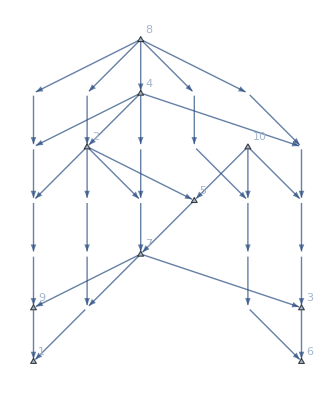

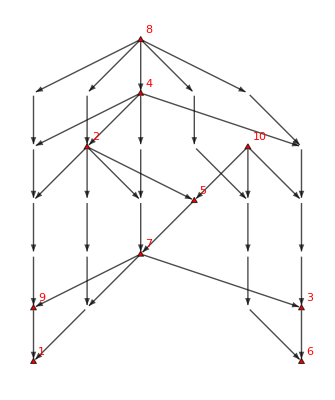

```mathematica
graphPlotNaive[step5]
graphPlotNaive[step5,VertexStyle->Red,EdgeStyle->Black]
```

## 6. Итоговая функция

```mathematica
??MyLayeredGraphPlot
```

Done GetDag

Done GetLayering

Done GetAddDummyVertics

Done GetVertexOrder

Done GetCoords

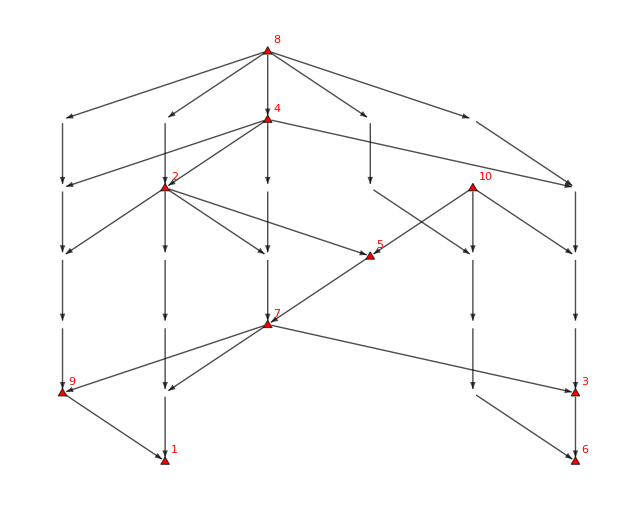

```mathematica
input=<|
"GetDag"-><|"ApproachOption"->"Cycle Removal"|>, 
"GetLayering"-> <|"ApproachOption"->"Longest Path",
                                    "ImprovmentOption"->False|>,
"AddDummyVertices"-><|"ApproachOption"->"Cut"|>,
"GetVertexOrder"-><|"ApproachOption"->{"Barycenter",5}|>,
"GetCoordinates"-> <|"YDistanceOption"->1,
                                           "XDistanceOption"->1.5,
                                            "WeightsOption"->{1,1,1}|>
|>;
res=MyLayeredGraphPlot[g,input,ApproachOption->"Naive"]
```